## Quantum Arithmetic

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Quantum Fourier Transform

Phase Basis

### The Discrete Fourier Transform

The discrete Fourier transform is a mathematical transformation that is very useful in processing data. It has many applications and is often employed when one wants to analyze signals over time.

This transformation on a list of N numbers is given by the so-called Fourier matrix of size N. For example, the Fourier matrix of size 4 looks like:

```mathematica
2*FourierMatrix[4]//MatrixForm
```

(1 | 1 | 1 | 1
1 | ⅈ | -1 | -ⅈ
1 | -1 | 1 | -1
1 | -ⅈ | -1 | ⅈ)

Recall that quantum states of n qubits can be represented by a list of 2^n complex amplitudes. For example, 8 complex amplitudes describe 3 qubits:

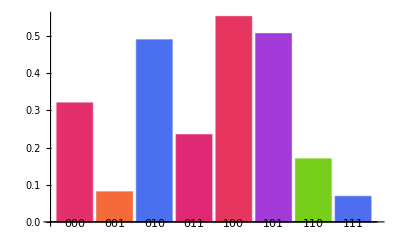

```mathematica
QuantumState["RandomPure"[3]]["AmplitudesPlot"]
```

The last lesson introduced the concept of asymptotic advantage, which many quantum algorithms enjoy over their classical counterparts. The most naive way to implement the classical discrete fourier transform on a list of 2^n complex data points requires O(2^(2n)) operations. However, there are other methods known as Fast Fourier Transforms. These faster methods only require O(n 2^n) classical operations.

Because 2^n complex data points can be encoded in only n qubits, the quantum Fourier transform requires only O(n^2) quantum gates to be applied to these n qubits.

The circuit to implement such a transformation on three qubits is given below:

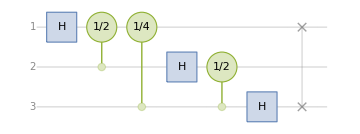

```mathematica
exampleQFT=QuantumCircuitOperator["Fourier"[3]];
exampleQFT["Diagram"]
```

Note the SWAP operation at the end; these are present so that the operator’s matrix elements are identical to the Fourier matrix of the appropriate size. Depending on the conventions for encoding the classical information, the SWAP operations may or may not appear in other texts.

```mathematica
exampleQFT["Matrix"]==FourierMatrix[2^3]
```

True

### Phase Basis Encoding

As you know from previous lessons, the computational basis is not the only way to encode classical information in a quantum state. Recall that the relative phase between two states can be experimentally distinguished. Thus, even if two states have the same probability to obtain outcomes in the computational basis, they are not the same state and will give different probabilities for outcomes in some other basis.

Consider two states who only differ by a relative phase difference between computational basis states:

```mathematica
ψ1=QuantumState["UniformSuperposition"];
ψ2=QuantumOperator["Phase"[θ]]@ψ1;
```

The probabilities in the computational basis are identical:

```mathematica
Simplify[ψ1["ProbabilitiesList"]==ψ2["ProbabilitiesList"],θ∈Reals]
```

True

However, the state really does change due to the phase rotation. You can see the effect in the Bloch plot below:

```mathematica
With[{ψ=QuantumCircuitOperator[{"UniformSuperposition","Phase"[phase]},"Parameters"->phase][]},
Manipulate[ψ[θ]["BlochPlot",PlotLabel->"θ_phase = "<>ToString@θ],{θ,0,2Pi},ControlPlacement->Top,TrackedSymbols:>θ,Initialization:>Needs["Wolfram`QuantumFramework`"]]
]
```

With this in mind, what happens after you perform a quantum Fourier transform on various input states? Explore the following tabs to find out:

```mathematica
TabView@Table[z->Rasterize@QuantumCircuitOperator["PhaseNumber"[z,3]][]["AmplitudesChart",ChartLegends->Automatic,ChartLabels->None,PlotLabel->"Input: "<>ToString@TraditionalForm@IntegerString[z,2,3]<>"\nOutput: "],{z,0,7}]
```

12345678

As you can see from the changing colors in the above plot, the information of the input state is transferred to information about the relative phases of each qubit (with respect to a uniform superposition in the computational basis).

The phases of each qubit follow a very specific pattern, which you can explore using the tabs below:

```mathematica
TabView@Table[z->With[{ψ=QuantumCircuitOperator[{IntegerString[z,2,3],"Fourier"[3]}][]},Labeled[Rasterize@GraphicsRow[Table[QuantumPartialTrace[ψ,Drop[Range[3],{k}]]["BlochPlot",PlotLabel->StringTemplate["θ_(`s`) = (2  π·`p`·`n`)/8"][<|"s"->3-k,"p"->2^(3-k),"n"->z|>]],{k,3}],Frame->All],Style["⟸  Most Significant\tLeast Significant  ⟹","Subsubsection"],Top]
],{z,0,7}]
```

12345678

Each possible input state gives a unique combination of phase rotations to the qubits, weighted by how significant that qubit should be when interpreting the measurement outcomes as a binary number. (In other words, the digit “1” in the string “100” is more significant than the digit “1” in the string “010”.)

But how do you “read out” this phase information if all the measurements are performed in the computational basis? If you simply try to measure, the information encoded in the qubit phases is lost:

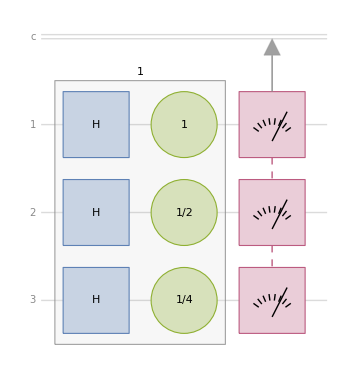

```mathematica
noInfoCircuit=QuantumCircuitOperator[{"PhaseNumber"[1,3],"M"->Range[3]}];
noInfoCircuit["Diagram"]
```

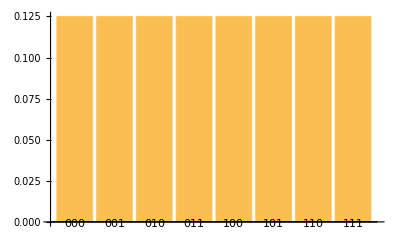

```mathematica
noInfoCircuit[]["ProbabilitiesPlot"]
```

As you can see from the plot, the phase information is not immediately accessible in the computational basis. Instead, you must perform the inverse of the quantum fourier transform, and then measure.

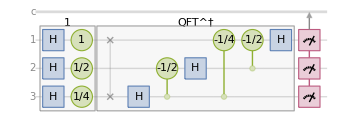

```mathematica
phaseInfoCircuit=QuantumCircuitOperator[{"PhaseNumber"[1,3],"InverseFourier"[3],"M"->Range[3]}];
phaseInfoCircuit["Diagram"]
```

By performing the inverse quantum Fourier transform, all of the phase information is now encoded in the computational basis. The measurement outcome is now the same as the number which was encoded in the phase basis:

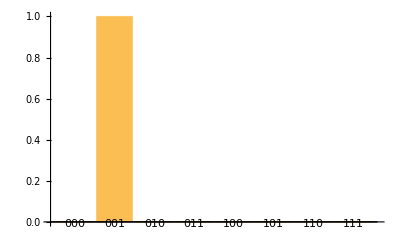

```mathematica
phaseInfoCircuit[]["ProbabilitiesPlot"]
```

With knowledge of the phase basis and the quantum fourier transform, you are now in a position to implement quantum circuits that carry out arithmetic.

### Quantum Phase Adders

When designing quantum circuits for arithmetic, it is important to distinguish between a circuit which performs the computation in-place as opposed to in a register. The in-place operation uses the same number of qubits as the input, but those qubits no longer encode the original input. In contrast, using a register requires more qubits to store the result, but the original qubits will still typically encode the original input when the algorithm is done.

As an example, let’s say you want to build a circuit which adds three to your input. This can be done using the pre-named "PhaseNumber" family of circuits. As with any digital computation, the arithmetic is performed modulo N, where N is the number of bits (or in this case qubits) used.

```mathematica
addThree[n_Integer]/;n>0:=QuantumCircuitOperator["PhaseNumber"[3,n,False],"Add(3)"]
```

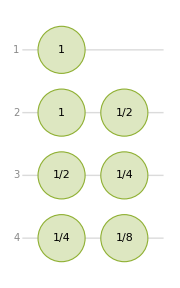

```mathematica
addThree[4]["Diagram",ImageSize->Small]
```

Let’s use this to compute 12+3 using four qubits:

```mathematica
qc1=With[{n=4},
QuantumCircuitOperator[{IntegerString[12,2,n],"Fourier"[n],addThree[n],"InverseFourier"[n],"M"->Range[n]}]
]
```

QuantumCircuitOperator[…]

This circuit first performs a quantum Fourier transform to get the input information into the phase basis, then applies an operation to add 3 in the phase basis, then performs an inverse quantum Fourier transform, and finally measures the results:

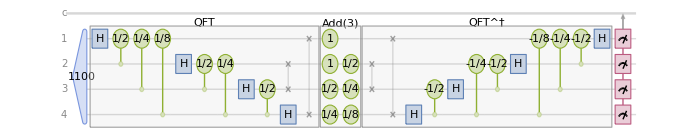

```mathematica
qc1["Diagram",ImageSize->700]
```

```mathematica
qc1[]["Probability"]
```

<|1111→1|>

With probability 1, this circuit gives the state corresponding to 15, the correct result for 12+3.

Note that with this kind of in-place operation, the circuit can only add 3 to the inputs. It cannot add any other number without changing the gates. However, it is possible for the input to be a superposition of states.

For example, suppose you didn’t know whether you wanted your input to be 6 or 4. You can run both computations at the same time using the previous type of circuit:

```mathematica
ψInputSuperposition=QuantumState[QuantumState["0110"]+QuantumState["0100"],"Label"->"ψ_6+ψ_4"]["Normalize"];
ψInputSuperposition["Formula"]
```

1/(√2)0100+1/(√2)0110

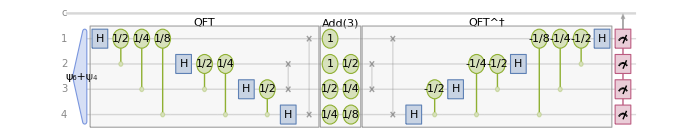

```mathematica
qc2=QuantumCircuitOperator[{ψInputSuperposition,"Fourier"[4],addThree[4],"InverseFourier"[4],"M"->Range[4]}];
qc2["Diagram",ImageSize->700]
```

Since the input was a superposition of states corresponding to 4 and 6, the output will now be a superposition of states corresponding to 7 and 9:

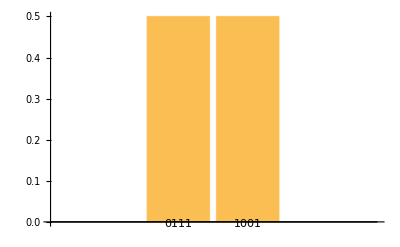

```mathematica
N[qc2][]["ProbabilityPlot"]
```

### Arbitrary Addition

While a circuit that can add superpositions of numbers to a specific number is already useful for quantum parallelization, you might instead be interested to have a circuit with fixed gates which can add any numbers between 0 and 2^n. This can be implemented as follows:

```mathematica
Clear[adderBlock]
```

```mathematica
adderBlock[n_Integer/;n>0]:=
QuantumCircuitOperator[
Table["C"[Table["PhaseShift"[1+a-b]->2n+1-b,{b,a}],{a}],{a,n}],
"Σ"
]
```

As before, the quantum Fourier transform and inverse quantum Fourier transform are utilized as part of the full circuit:

```mathematica
Clear[qftAdder]
```

```mathematica
qftAdder[n_Integer/;n>0]:=QuantumCircuitOperator[{
"Fourier"[n]->Range[n+1,2 n],
adderBlock[n],
"InverseFourier"[n]->Range[n+1,2 n]
},"QFT Adder"]
```

A circuit to add 2+2 would then look like this:

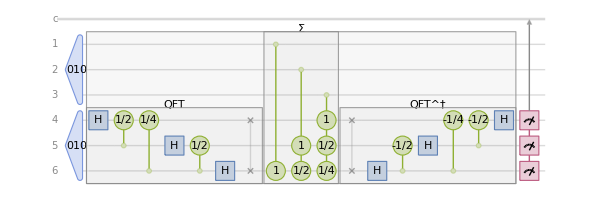

```mathematica
qc3=QuantumCircuitOperator[{
"010"->{1,2,3},
"010"->{4,5,6},
QuantumCircuitOperator[qftAdder[3],"ShowLabel"->False],
"M"->{4,5,6}
}];
qc3["Diagram",ImageSize->600,Expand->2]
```

With probability 1, the measured outcome of this circuit gives the state corresponding to 4 when the input states both correspond to 2.

```mathematica
qc3[]["Probability"]
```

<|100→1|>

### Circuits for Multiplication

Multiplication can be achieved through repeated addition. When multiplying two numbers representable with n bits, the result can always be represented with 2n bits. Since you are now working with a larger register, you can be more efficient with gates by introducing a circuit element that has the effect of adding not just an input, but adding 2^k times that input.

You could define such a circuit element as follows:

```mathematica
Clear[kAdderBlock]
```

```mathematica
kAdderBlock[n_Integer,Optional[k_Integer,0]]/;n>0&&n>=k>=0:=
QuantumCircuitOperator[
Table["C"[Table["PhaseShift"[1+n+a-b-k]->3n+1-b,{b,a+n-k}],{a}],{a,n}],
StringTemplate["2^(`k`)Σ"][<|"k"->k|>]]
```

A circuit to add 2+4×2 would then look like this:

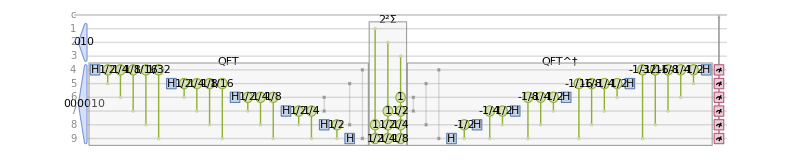

```mathematica
qc4=QuantumCircuitOperator[{
"010"->{1,2,3},
"000010"->{4,5,6,7,8,9},
"Fourier"[6]->{4,5,6,7,8,9},
kAdderBlock[3,2],
"InverseFourier"[6]->{4,5,6,7,8,9},
"M"->{4,5,6,7,8,9}
}];
qc4["Diagram",ImageSize->800,Expand->2]
```

As expected, 2+4×2=10, represented in binary:

```mathematica
N[qc4][]["Probability"]
```

<|001010→1.|>

A multiplication circuit would then use these blocks, controlled by bits from another register. A possible implementation looks like this:

```mathematica
Clear[mulBlock]
```

```mathematica
mulBlock[n_Integer]/;n>0:=
QuantumCircuitOperator[
Flatten@Table["C"[Table["PhaseShift"[1+i1+i2-r]->4n+1-r,{r,i1+i2}],{i1,i2+n}],{i1,n},{i2,n}],
"Π"]
```

```mathematica
Clear[qftMul]
```

```mathematica
qftMul[n_Integer]/;n>0:=
QuantumCircuitOperator[{
"Fourier"[2n]->Range[2n+1,4n],
mulBlock[n],
"InverseFourier"[2n]->Range[2n+1,4n]
},"QFT Multiplier"]
```

A circuit that multiplies 3×3 would then look like this:

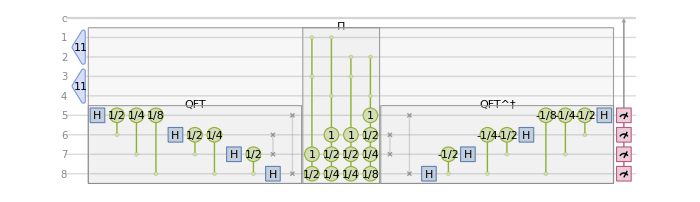

```mathematica
qc5=QuantumCircuitOperator[{
"11"->{1,2},
"11"->{3,4},
QuantumCircuitOperator[qftMul[2],"ShowLabel"->False],
"M"->{5,6,7,8}
}];
qc5["Diagram",ImageSize->700,Expand->2]
```

As expected, you get 9 with 100% probability when running this circuit:

```mathematica
N[qc5][]["Probability"]
```

<|1001→1.|>

You can define a function to check that this works in general:

```mathematica
Clear[checkercirc]
```

```mathematica
checkercirc=N@QuantumCircuitOperator[{
IntegerString[#1,2,2]->{1,2},
IntegerString[#2,2,2]->{3,4},
QuantumCircuitOperator[qftMul[2],"ShowLabel"->False],
"M"->{5,6,7,8}
}]&;
```

Apply the function to all integer pairs that can be expressed with two bits:

```mathematica
Grid[Table[i*j->First@Keys[checkercirc[i,j][]["Probability"]],{i,0,3},{j,0,3}],Spacings->{1,1},Frame->All]//EchoTiming
```

36.3905

0→0000 | 0→0000 | 0→0000 | 0→0000
0→0000 | 1→0001 | 2→0010 | 3→0011
0→0000 | 2→0010 | 4→0100 | 6→0110
0→0000 | 3→0011 | 6→0110 | 9→1001

As you can see, this circuit works as it should. You can also try with larger integers:

```mathematica
Module[{n=3,qc},
qc=QuantumCircuitOperator[{
"011"->Range[n],
"101"->Range[n+1,2n],
QuantumCircuitOperator[qftMul[n],"ShowLabel"->False],
"M"->Range[2n+1,4n]
}];
N[qc][]["Probability"]
]
```

<|001111→1.|>

Notice that this implementation used double-controlled gates. If you need only 2-qubit gates for practical engineering reasons, the decomposition of the circuit will be more complicated.

### Finding Primes

Using the multiplication circuit, imagine the following experiment:

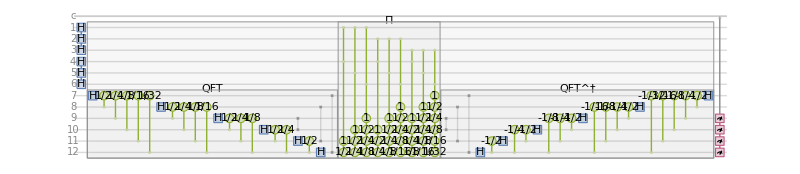

```mathematica
qc7=With[{n=3},QuantumCircuitOperator[{
"H"->Range[n],
"H"->Range[n+1,2n],
QuantumCircuitOperator[qftMul[n],"ShowLabel"->False],
"M"->Range[3n,4n]
}]];
qc7["Diagram",ImageSize->800,Expand->2]
```

The circuit above performs all multiplications of integers from 0 to 7. Then, the result modulo 16 is returned.

What happens if you simulated the measurements from this experiment? For this particular random seed, notice that you eventually discover “gaps” in the results which correspond to the primes 11 and 13. However, this particular method very nearly missed that 15 is composite, as the simulated experiment returned this result only once (due to randomness in the measurement outcomes).

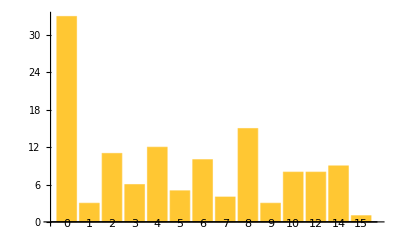

```mathematica
SeedRandom[321];BarChart[
KeySort@CountsBy[
N[qc7][]["SimulatedMeasurement",128],
FromDigits[First@#,2]&
],ChartLabels->Automatic
]
```